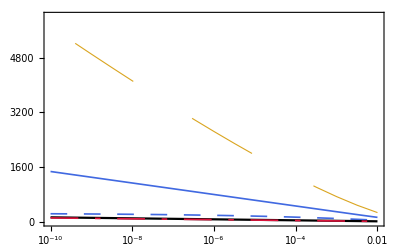

```mathematica
(*This file contains the code used to plot the overhead of magic state distillation in Fig.2 in [arXiv:2307.08258
]*)
ClearAll["Global`*"]
(*Magic monotones based on the α-z Rényi divergences between two depolarized states with parameters r and q*)
Dα[α_,r_,q_]:=If[α==1,1,(1/(α-1))*Log2[((1+r)/2)^α*((1+q)/2)^(1-α)+((1-r)/2)^α*((1-q)/2)^(1-α)]];

(*Depolarizing parameter of the initial state*)
r=3/4;

(*Bound on the number of copies given by the Dmin bound as a function of the distillation error ϵ and the probability p*)
Rate[ϵ_,p_]:=Module[{t},t=ϵ;
q:=1-2*ϵ;
(4 Log[1-p+ⅇ^(1/4 (-((-2+√2) Log[(2 (-1+q))/(-2+√2)])+(2+√2) Log[(2 (1+q))/(2+√2)])) p])/(Log[16]-2 Log[2-√2]+√2 Log[2-√2]-2 Log[2+√2]-√2 Log[2+√2]-(-2+√2) Log[1-r]+(2+√2) Log[1+r])]

(*Projective robustness and weight bounds*)
ProjRob[ϵ_]:=Log[1.2010,((1-ϵ)/ϵ)*((1-0.8536)/0.8536)]
Weight[ϵ_]:=Log[1.1716,((1-0.8536)/ϵ)]

(*Plot of the Dmin bounds for p=1,0.4 and the weight and projective robustness bounds*)
p1=LogLinearPlot[{Rate[ϵ,1],Rate[ϵ,0.4],Weight[ϵ],ProjRob[ϵ]},{ϵ,10^(-10),10^(-2)},PlotRange->{0,6000},Frame->True,PlotStyle->{Directive[RGBColor[65/255,105/255,225/255],Automatic,Thickness[0.003]],Directive[RGBColor[65/255,105/255,225/255],Dashing[{0.03}],Thickness[0.003]],Directive[Black,Automatic,Thickness[0.004]],Directive[RGBColor[220/255,20/255,60/255],Dashing[{0.05,0.03,0.01,0.03}],Thickness[0.003]]},FrameTicks->{Automatic,Table[i,{i,0,6000,800}]},TicksStyle->Directive[FontSize->40],LabelStyle->{FontSize->8,FontFamily->"Times",Black}];

(*Plot of the Drev bound*)
p2=ListLogLinearPlot[{Table[{N@10^(-δ),First[NMaximize[{Dα[x,1/Sqrt[2],1-2*10^(-δ)]/Dα[x,1/Sqrt[2],r],x>0},x]]},{δ,2,10,0.5}]},Joined->True,Frame->True,PlotStyle->{Directive[RGBColor[218/255,165/255,32/255],Thickness[0.002],Dashing[{5}]]},TicksStyle->Directive[FontSize->40],LabelStyle->{FontSize->7.3,FontFamily->"Times",Black},FrameTicks->{Automatic,Table[i,{i,0,6000,800}]},PlotRange->{0,6000}];
Show[p1,p2]
```